```mathematica
<<UNET`
```

## Generated Data

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Show UNET

```mathematica
(*4 input channels, 8 classes, dimensions 2D - (32x)160x160}*)
```

```mathematica
lab=Style[#,{Bold,TextAlignment->Center}]&/@{"Features in\nfirst Layer", "# Array Elements\nUNET blocks", "# Array Elements\nResNet blocks"};
```

```mathematica
dim2D={160,160};
dim3D={32,160,160};
{nchan,nclass}={4,8};
```

```mathematica
par2D=Table[
net12D=UNET[nchan,nclass, i,dim2D,BlockType->"UNET" ];
net22D=UNET[nchan,nclass, i,dim2D,BlockType->"ResNet" ];
Flatten@{i,NetInformation[net12D,{"ArraysTotalElementCount"}],NetInformation[net22D,{"ArraysTotalElementCount"}]}
,{i,Range[4,32,4]}];
lay1=NetInformation[net12D,{"LayersCount"}][[1]];
lay2=NetInformation[net22D,{"LayersCount"}][[1]];
tab1=Column[{Style["2D UNET\nLayers UNET: "<>ToString[lay1]<>" - Layers ResNet: "<>ToString[lay2],{Bold,14,TextAlignment->Center}],
TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Center]},Alignment->Center];
```

```mathematica
par3D=Table[
net13D=UNET[nchan,nclass, i,dim3D,BlockType->"UNET" ];
net23D=UNET[nchan,nclass, i,dim3D,BlockType->"ResNet" ];
Flatten@{i,NetInformation[net13D,{"ArraysTotalElementCount"}],NetInformation[net23D,{"ArraysTotalElementCount"}]}
,{i,Range[4,32,4]}];
lay1=NetInformation[net13D,{"LayersCount"}][[1]];
lay2=NetInformation[net23D,{"LayersCount"}][[1]];
tab2=Column[{Style["3D UNET\nLayers UNET: "<>ToString[lay1]<>" - Layers ResNet: "<>ToString[lay2],{Bold,14,TextAlignment->Center}],
TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Center]},Alignment->Center];
```

```mathematica
Row[{tab1,tab2},"                 "]
```

2D UNET
Layers UNET: 81 - Layers ResNet: 135
Features in
first Layer | # Array Elements
UNET blocks | # Array Elements
ResNet blocks
4 | 124604 | 31804
8 | 494576 | 121536
12 | 1109924 | 269204
16 | 1970648 | 474808
20 | 3076748 | 738348
24 | 4428224 | 1059824
28 | 6025076 | 1439236
32 | 7867304 | 18765843D UNET
Layers UNET: 109 - Layers ResNet: 163
Features in
first Layer | # Array Elements
UNET blocks | # Array Elements
ResNet blocks
4 | 369980 | 62476
8 | 1476080 | 244224
12 | 3318308 | 545252
16 | 5896664 | 965560
20 | 9211148 | 1505148
24 | 13261760 | 2164016
28 | 18048500 | 2942164
32 | 23571368 | 3839592

```mathematica
UNET[4,14,32,{128,128}]
```

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1}=SplitTrainData[data1,label1];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*visualize the test data*)
ShowChannelClassData[testData1,testLabel1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->2]
```

-Graphics- | -Graphics- | -Graphics-

channels: 1 - classes: 1 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.996}

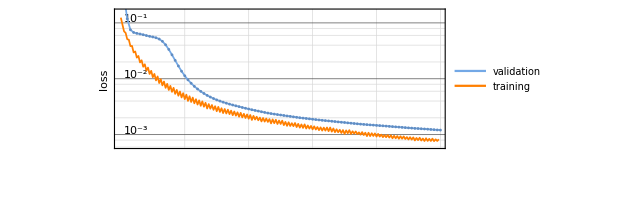

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{plots1,result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->8];
plots1
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2}=SplitTrainData[data2,label2];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{plots2,result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->8];
plots2
```

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.999,2→0.994}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[150,3];
```

```mathematica
(*data augmentation, increase the data by flipping and rotating*)
(*visualize the flips and rotations*)
data3R=RotateFlip[data3[[1;;2]]];
label3R=RotateFlip[label3[[1;;2]]];
ShowChannelClassData[data3R,label3R, NumberRowItems->4,MakeDifferenceImage->False,StepSize->1,ImageSize->100]
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3}=SplitTrainData[data3,label3,AugmentTrainData->False];
```

Dimensions data: {150,1,128,128} - Dimensions label: {150,128,128}

Nuber of Samples in each set: {105,30,15}

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{plots3,result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->16,BatchSize->64,BlockType->"ResNet"];
trained3
(*train the net*)
{{net3b,trained3b,netTrained3b},{plots3b,result3b,iou3b}}=TrainUNET[train3,valid3,{testData3,testLabel3},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->16,BatchSize->64,BlockType->"UNET"];
trained3b
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3b, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4}=SplitTrainData[data4,label4];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{plots4,result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->16,BatchSize->64,BlockType->"ResNet"];
trained4
(*train the net*)
{{net4b,trained4b,netTrained4b},{plots4b,result4b,iou4b}}=TrainUNET[train4,valid4,{testData4,testLabel4},
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->16,BatchSize->64,BlockType->"UNET"];
trained4b
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4b, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5}=SplitTrainData[data5,label5];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
im=8;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;

(*train the net with monitor function*)
{{net,trained,netTrained},{plots,result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5}, TargetDevice->{"GPU",1},MaxTrainingRounds->50,NetParameters->32,
TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Batches"]}];
```

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.999,2→0.994,3→0.997,4→0.99}

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];
```

```mathematica
(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```

D:\Werk\Research\DTITools\machine learning\animv2.gif